### 1

```mathematica
xDot[x_,y_,μ_] := μ x - 3y -x^3;
yDot[x_,y_,μ_] := 3x + μ y + 2y^3;
```

#### μ negative

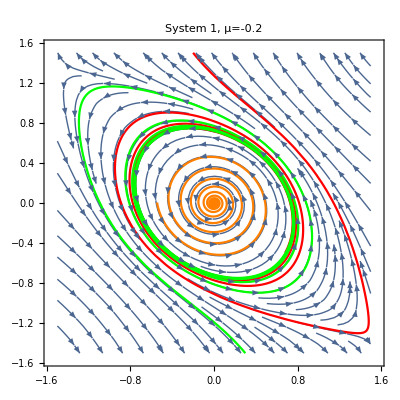

/Users/adam/Programming/CAS/DynamicalSystems/Assignment 2/hopf_1_neg.png

/Users/adam/Programming/CAS/DynamicalSystems/Assignment 2/hopf_1_neg.png

```mathematica
scale = 1.5;
μ=-0.2;

x0=-0.2;
y0=1.5;
tMax=0;
tMin=-10;
sol = NDSolve[{x'[t]==xDot[x[t],y[t],μ],y'[t]==yDot[x[t],y[t],μ], x[0]==x0,y[0]==y0},{x[t],y[t]},{t,tMin,tMax}];
p1 = ParametricPlot[{x[t],y[t]}/.sol,{t,tMin,tMax}, PlotStyle->Red];

x0=0.3;
y0=-1.5;
tMax=0;
tMin=-10;
sol = NDSolve[{x'[t]==xDot[x[t],y[t],μ],y'[t]==yDot[x[t],y[t],μ], x[0]==x0,y[0]==y0},{x[t],y[t]},{t,tMin,tMax}];
p2 = ParametricPlot[{x[t],y[t]}/.sol,{t,tMin,tMax}, PlotStyle->Green];

x0=0.01;
y0=0;
tMax=0;
tMin=-22;
sol = NDSolve[{x'[t]==xDot[x[t],y[t],μ],y'[t]==yDot[x[t],y[t],μ], x[0]==x0,y[0]==y0},{x[t],y[t]},{t,tMin,tMax}];
p3 = ParametricPlot[{x[t],y[t]}/.sol,{t,tMin,tMax}, PlotStyle->Orange];

p4 =StreamPlot[{xDot[x,y,μ],yDot[x,y,μ]},{x,-scale,scale},{y,-scale,scale}, PlotLabel->StringForm["System 1, μ=``",μ]];
g = Show[{p4,p1,p2,p3}]
Export["/Users/adam/Programming/CAS/DynamicalSystems/Assignment 2/hopf_1_neg.png",g,"PNG", ImageSize->1500]
```

#### μ positive

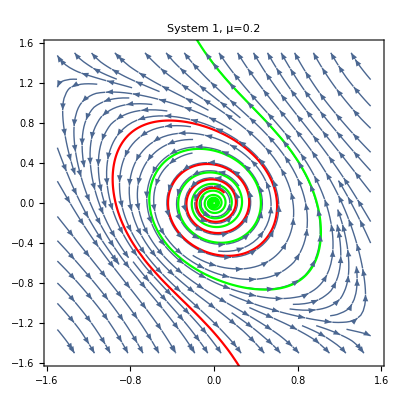

/Users/adam/Programming/CAS/DynamicalSystems/Assignment 2/hopf_1_pos.png

```mathematica
scale = 1.5;
μ=0.2;

x0=0.01;
y0=0.01;
tMax=19.2;
sol = NDSolve[{x'[t]==xDot[x[t],y[t],μ],y'[t]==yDot[x[t],y[t],μ], x[0]==x0,y[0]==y0},{x[t],y[t]},{t,0,tMax}];
p1 = ParametricPlot[{x[t],y[t]}/.sol,{t,0,tMax}, PlotStyle->Green];

x0=0.1;
y0=0.1;
tMax=7.7;
sol = NDSolve[{x'[t]==xDot[x[t],y[t],μ],y'[t]==yDot[x[t],y[t],μ], x[0]==x0,y[0]==y0},{x[t],y[t]},{t,0,tMax}];
p2 = ParametricPlot[{x[t],y[t]}/.sol,{t,0,tMax}, PlotStyle->Red];

p4 =StreamPlot[{xDot[x,y,μ],yDot[x,y,μ]},{x,-scale,scale},{y,-scale,scale}, PlotLabel->StringForm["System 1, μ=``",μ]];
g=Show[{p4,p1,p2}]
Export["/Users/adam/Programming/CAS/DynamicalSystems/Assignment 2/hopf_1_pos.png",g,"PNG", ImageSize->1500]
```

### 2

```mathematica
μ=.
xDot[x_,y_,μ_] := μ x +y -x^2;
yDot[x_,y_,μ_] := -x + μ y + 2x^2;
(*scale = 1;
tab = Table[StreamPlot[{xDot[x,y,μ],yDot[x,y,μ]},{x,-scale,scale},{y,-scale,scale}, PlotLabel->StringForm["μ=``",μ]],{μ,{-0.1,0,0.1}}];
GraphicsRow[tab]*)
```

#### μ negative

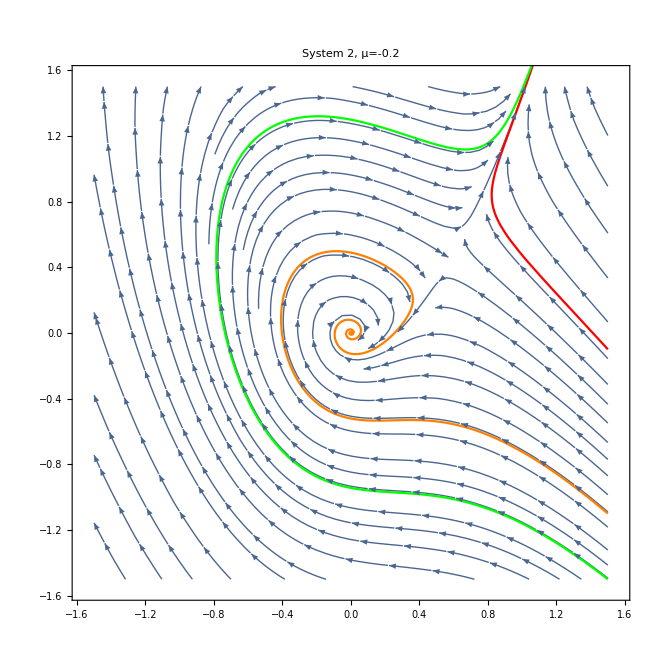

/Users/adam/Programming/CAS/DynamicalSystems/Assignment 2/hopf_2_neg.png

```mathematica
scale = 1.5;
μ=-0.2;

x0=1.5;
y0=-0.1;
tMax=15;
sol = NDSolve[{x'[t]==xDot[x[t],y[t],μ],y'[t]==yDot[x[t],y[t],μ], x[0]==x0,y[0]==y0},{x[t],y[t]},{t,0,tMax}];
p1 = ParametricPlot[{x[t],y[t]}/.sol,{t,0,tMax}, PlotStyle->Red];

x0=1.5;
y0=-1.5;
tMax=15;
sol = NDSolve[{x'[t]==xDot[x[t],y[t],μ],y'[t]==yDot[x[t],y[t],μ], x[0]==x0,y[0]==y0},{x[t],y[t]},{t,0,tMax}];
p2 = ParametricPlot[{x[t],y[t]}/.sol,{t,0,tMax}, PlotStyle->Green];

x0=1.5;
y0=-1.1;
tMax=100;
sol = NDSolve[{x'[t]==xDot[x[t],y[t],μ],y'[t]==yDot[x[t],y[t],μ], x[0]==x0,y[0]==y0},{x[t],y[t]},{t,0,tMax}];
p3 = ParametricPlot[{x[t],y[t]}/.sol,{t,0,tMax}, PlotStyle->Orange];

p4 =StreamPlot[{xDot[x,y,μ],yDot[x,y,μ]},{x,-scale,scale},{y,-scale,scale}, PlotLabel->StringForm["System 2, μ=``",μ]];
g=Show[{p4,p1,p2,p3}]
Export["/Users/adam/Programming/CAS/DynamicalSystems/Assignment 2/hopf_2_neg.png",g,"PNG", ImageSize->1500]
```

#### μ positive

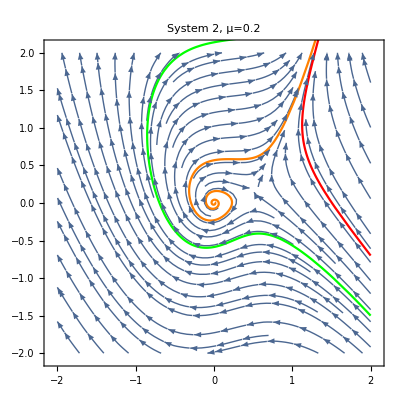

/Users/adam/Programming/CAS/DynamicalSystems/Assignment 2/hopf_2_pos.png

```mathematica
scale = 2;
μ=0.2;

x0=2;
y0=-0.7;
tMax=15;
sol = NDSolve[{x'[t]==xDot[x[t],y[t],μ],y'[t]==yDot[x[t],y[t],μ], x[0]==x0,y[0]==y0},{x[t],y[t]},{t,0,tMax}];
p1 = ParametricPlot[{x[t],y[t]}/.sol,{t,0,tMax}, PlotStyle->Red];

x0=2;
y0=-1.5;
tMax=12;
sol = NDSolve[{x'[t]==xDot[x[t],y[t],μ],y'[t]==yDot[x[t],y[t],μ], x[0]==x0,y[0]==y0},{x[t],y[t]},{t,0,tMax}];
p2 = ParametricPlot[{x[t],y[t]}/.sol,{t,0,tMax}, PlotStyle->Green];

x0=0.01;
y0=0.01;
tMax=30;
sol = NDSolve[{x'[t]==xDot[x[t],y[t],μ],y'[t]==yDot[x[t],y[t],μ], x[0]==x0,y[0]==y0},{x[t],y[t]},{t,0,tMax}];
p3 = ParametricPlot[{x[t],y[t]}/.sol,{t,0,tMax}, PlotStyle->Orange];

p4 =StreamPlot[{xDot[x,y,μ],yDot[x,y,μ]},{x,-scale,scale},{y,-scale,scale}, PlotLabel->StringForm["System 2, μ=``",μ]];
g=Show[{p4,p1,p2,p3}]
Export["/Users/adam/Programming/CAS/DynamicalSystems/Assignment 2/hopf_2_pos.png",g,"PNG", ImageSize->1500]
```